## Details of the Magnitude System

## Preliminaries

If all we had to worry about were bolometric fluxes, then the magnitude system would be pretty simple. Unfortunately, the real world is much more complicated than that.  Not only do different stars have the peak of their spectra at different frequencies, but also the equipment we use to measure the spectrum has peaks and dips in sensitivity, as does the absorption of the atmosphere, means that the amount of energy in a given energy range is actually a “convolution” of multiple functions.

We will build up to this more complex situation starting with an idealization: that the spectrum of a star is a black-body given by a temperature.

Back in Chapter 4, we derived the black-body spectrum. One formula from that chapter is 4.4-5, which said that the energy per unit area coming off the surface of a black-body between ν and ν+Δν, is:

F_ν Δν=(2πhν^3/c^2)/(e^(hν/kT)- 1)Δν

As usual, I have put a small frequency range Δν on both sides of the equation because that makes the equation agree with the sentence preceding it. You are welcome to cancel it off, in which case the interpretation is energy per unit area per unit frequency, which is slightly more abstract.

## Determining the Temperature of a Star

If a star can be approximated as a black-body, and if one can measure F at two different frequencies, then one will have:

F_ν_1=(2πhν_1^3/c^2)/(e^(hν_1/kT)- 1)

F_ν_2=(2πhν_2^3/c^2)/(e^(hν_2/kT)- 1)

Let us define x_1=(h ν_1)/kT and x_2=(h ν_2)/kT. Then

F_ν_1/F_ν_2=(x_1^3(e^x_2-1))/(x_2^3(e^x_1-1))

So suppose one has done that measurement, and has the ratio. Can one solve for T?

Let’s define two more things: T_1=hν_1/k and T_2=hν_2/k. Then x_1=T_1/T and x_2=T_2/T.

F_ν_1/F_ν_2=(T_1^3(e^(T_2/T)-1))/(T_2^3(e^(T_1/T)-1))

Let’s graph this as a function of T for four different values of T_1 and T_2. How about T_2=T_1/10, T_2=3T_1/4, T_2=4T_1/3, and T_2=10 T_1. To put it in words, the four cases are, T_2 a lot less than T_1, a bit less, a bit more, and a lot more. In all four cases, we can write T_2=r T_1, and the four cases are r=1/10, r=3/4, r=4/3, and r=10.

In all cases, I will plot T in units of T_1. In other words, we are scaling T_1 out of the problem.

```mathematica
family[t_, r_]:=1/r^3(Exp[rt]-1)/(Exp[t]-1);
```

```mathematica
aLotLess[t_]:=family[t, 1/10];
```

```mathematica
aLittleLess[t_]:=family[t, 3/4];
```

```mathematica
aLittleMore[t_]:=family[t, 4/3];
```

```mathematica
aLotMore[t_]:=family[t, 10];
```

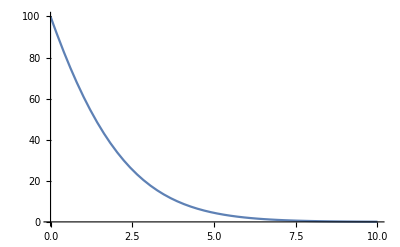

```mathematica
Plot[aLotLess[t],{t, 0,10}]
```

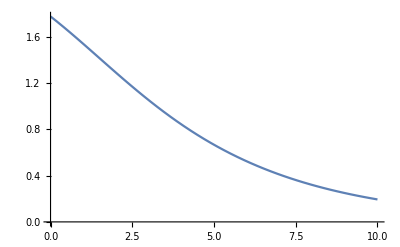

```mathematica
Plot[aLittleLess[t],{t, 0,10}]
```

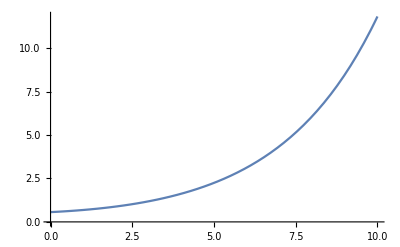

```mathematica
Plot[aLittleMore[t],{t, 0,10}]
```

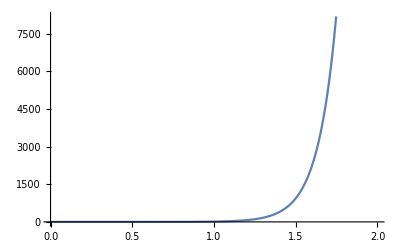

```mathematica
Plot[aLotMore[t],{t, 0,2}]
```

This exercise allowed me to become more familiar with the family of functions, to convince myself that in all cases, the function is monotonic and wide-ranging, and to learn that it is a bad idea to scale out T_1 in the last case, when T_1 is the much larger temperature, because the result ends up extremely strongly dependent on t. If T_1 is much larger, scale out T_2 instead.

We have adequately verified Swihart’s statement (below Equation 6.2-6), that “a measurement of the flux ratio at any two frequencies then allows x, and therefore T, to be determined.”

## Magnitude Definitions

Last time we had no problem verifying 6.3-1. Actually, Swihart states 6.3-1 like it was a definition. We began with the definition from Hipparcos as made quantitative by Pogson, which is that

F=A 100^(-m/5)

where A is some constant, and the -m/5 comes from the idea of Pogson that 5 magnitudes shall be a decrease in brightness of a factor of 100. Each single step increase of magnitude is 100^(-1/5), which turns out to be a decrease by a factor of 2.512.

Taking log base 10 of both sides of the equation, we have little trouble getting

m=C-5/2 log F

The relationship between C and A is

C=5/2 log A